```mathematica
times[x_]:=If[Length@x==1,x[[1]]^2,Times@@x]
```

```mathematica
divs=Table[{x,Length@Divisors[x],Length@Select[Subsets[Divisors[x]],times[#]==x&]},{x,2,300}];
```

```mathematica
TableForm[divs[[;;100]],TableHeadings->{None,{"n","divisors","combinations"}}]
```

n | divisors | combinations
2 | 2 | 1
3 | 2 | 1
4 | 3 | 2
5 | 2 | 1
6 | 4 | 3
7 | 2 | 1
8 | 4 | 3
9 | 3 | 2
10 | 4 | 3
11 | 2 | 1
12 | 6 | 5
13 | 2 | 1
14 | 4 | 3
15 | 4 | 3
16 | 5 | 4
17 | 2 | 1
18 | 6 | 5
19 | 2 | 1
20 | 6 | 5
21 | 4 | 3
22 | 4 | 3
23 | 2 | 1
24 | 8 | 9
25 | 3 | 2
26 | 4 | 3
27 | 4 | 3
28 | 6 | 5
29 | 2 | 1
30 | 8 | 9
31 | 2 | 1
32 | 6 | 5
33 | 4 | 3
34 | 4 | 3
35 | 4 | 3
36 | 9 | 10
37 | 2 | 1
38 | 4 | 3
39 | 4 | 3
40 | 8 | 9
41 | 2 | 1
42 | 8 | 9
43 | 2 | 1
44 | 6 | 5
45 | 6 | 5
46 | 4 | 3
47 | 2 | 1
48 | 10 | 13
49 | 3 | 2
50 | 6 | 5
51 | 4 | 3
52 | 6 | 5
53 | 2 | 1
54 | 8 | 9
55 | 4 | 3
56 | 8 | 9
57 | 4 | 3
58 | 4 | 3
59 | 2 | 1
60 | 12 | 17
61 | 2 | 1
62 | 4 | 3
63 | 6 | 5
64 | 7 | 8
65 | 4 | 3
66 | 8 | 9
67 | 2 | 1
68 | 6 | 5
69 | 4 | 3
70 | 8 | 9
71 | 2 | 1
72 | 12 | 17
73 | 2 | 1
74 | 4 | 3
75 | 6 | 5
76 | 6 | 5
77 | 4 | 3
78 | 8 | 9
79 | 2 | 1
80 | 10 | 13
81 | 5 | 4
82 | 4 | 3
83 | 2 | 1
84 | 12 | 17
85 | 4 | 3
86 | 4 | 3
87 | 4 | 3
88 | 8 | 9
89 | 2 | 1
90 | 12 | 17
91 | 4 | 3
92 | 6 | 5
93 | 4 | 3
94 | 4 | 3
95 | 4 | 3
96 | 12 | 19
97 | 2 | 1
98 | 6 | 5
99 | 6 | 5
100 | 9 | 10
101 | 2 | 1

```mathematica
comb=divs[[All,{2,3}]];
```

```mathematica
GroupBy[comb,First->Last,Union]
```

<|2→{1},3→{2},4→{3},6→{5},5→{4},8→{9},9→{10,12},10→{13},12→{17,19},7→{8},16→{29,31,33},15→{28},18→{35,41},14→{27},20→{49}|>

```mathematica
divs2=Table[{x,Length@Divisors[x],Length@Select[Subsets[Divisors[x]],times[#]==x&]},{x,2,500}];
```

```mathematica
comb2=divs2[[All,{2,3}]];
```

```mathematica
GroupBy[comb2,First->Last,Union]
```

<|2→{1},3→{2},4→{3},6→{5},5→{4},8→{9},9→{10,12},10→{13},12→{17,19},7→{8},16→{29,31,33,37},15→{28},18→{35,41},14→{27},20→{49,53},24→{61,67,75}|>

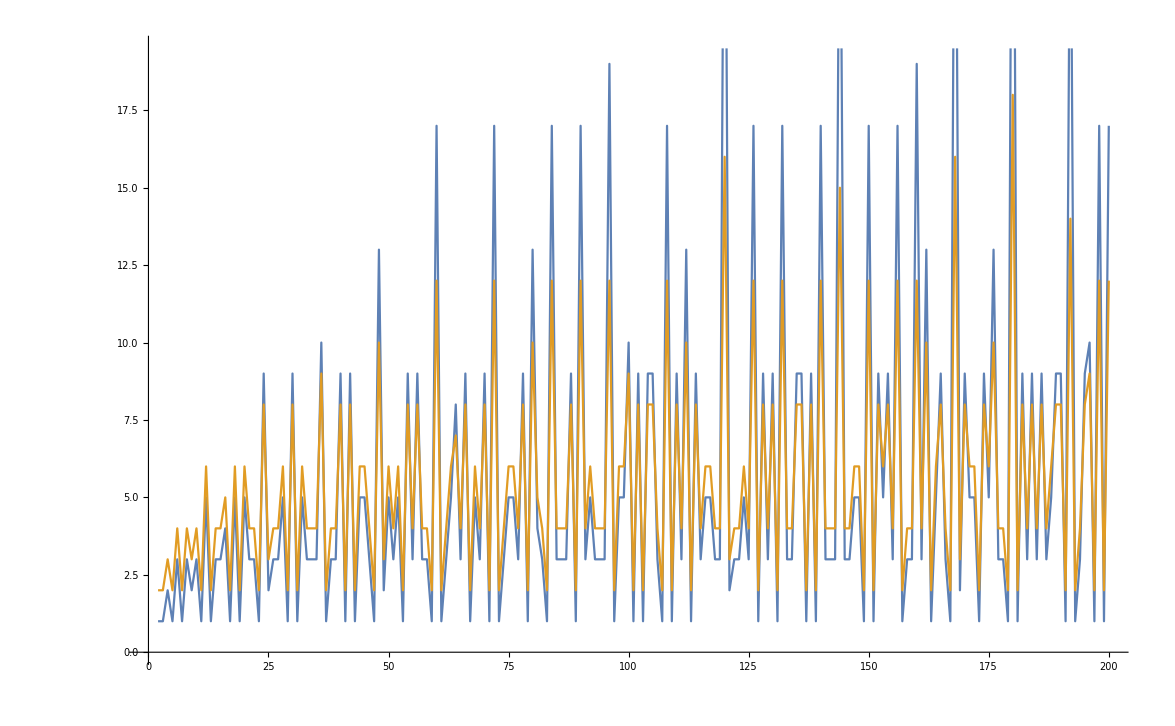

```mathematica
ListLinePlot[{Table[{x,Length@Select[Subsets[Divisors[x]],times[#]==x&]},{x,2,200}],Table[{x,Length@Divisors[x]},{x,2,200}]}]
```

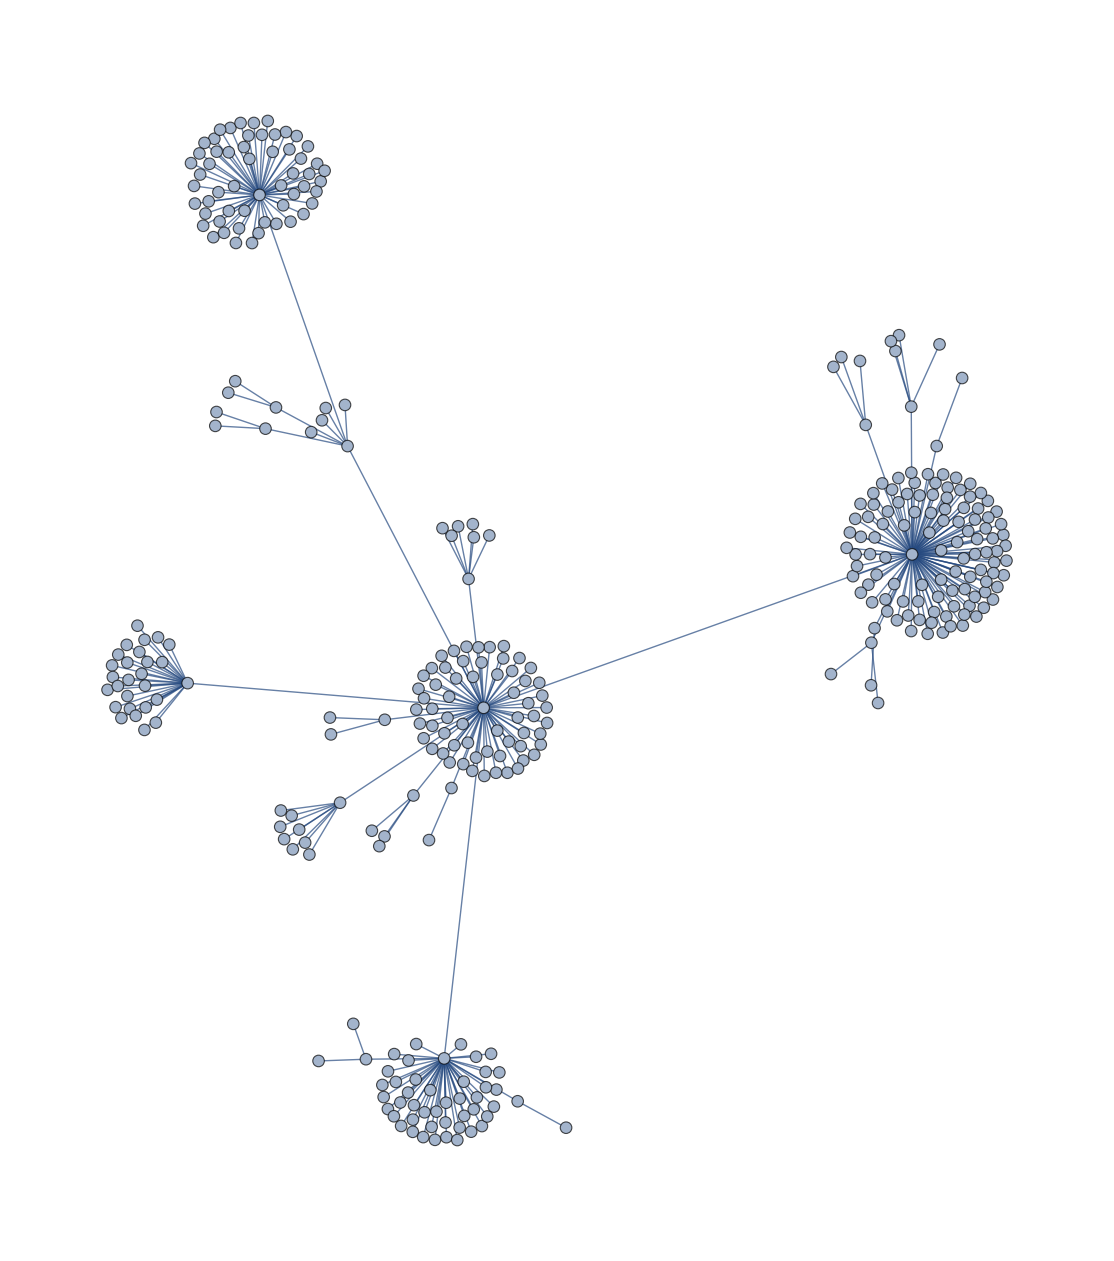

```mathematica
Graph[Table[{x,Length@Select[Subsets[Divisors[x]],times[#]==x&]},{x,2,350}],VertexLabels->Placed["Name",Tooltip]]
```